```mathematica
tauY=-2.8*10^(-5);
beta0Y=4.6461;
beta1Yl=0.0000151;
beta1Yr=beta1Yl+tauY;
beta2Yl=-5.69×10^(-9);
beta2Yr=beta2Yl+2.92×10^(-8);
beta3Yl=-1.07×10^(-12);
beta3Yr=beta3Yl-1.31×10^(-11);
beta4Yl=-8.49×10^(-17);
beta4Yr=beta4Yl+3.12×10^(-15);
beta5Yl=-2.65×10^(-21);
beta5Yr=beta5Yl-2.03×10^(-19);

tauB=-1.4*10^(-5);
beta0B=3.646943;
beta1Bl=0.0000103;
beta1Br=beta1Bl+tauB;
beta2Bl=-3.18×10^(-9);
beta2Br=beta2Bl+1.57×10^(-8);
beta3Bl=-5.72×10^(-13);
beta3Br=beta3Bl-5.60×10^(-12);
beta4Bl=-4.83×10^(-17);
beta4Br=beta4Bl+1.21×10^(-15);
beta5Bl=-1.42×10^(-21);
beta5Br=beta5Bl-7.29×10^(-20);

fYl[x_]:=beta0Y+beta1Yl x+beta2Yl x^2+beta3Yl x^3+beta4Yl x^4+beta5Yl x^5;
fYr[x_]:=beta0Y+beta1Yr x+beta2Yr x^2+beta3Yr x^3+beta4Yr x^4+beta5Yr x^5;

fBl[x_]:=beta0B+beta1Bl x+beta2Bl x^2+beta3Bl x^3+beta4Bl x^4+beta5Bl x^5;
fBr[x_]:=beta0B+beta1Br x+beta2Br x^2+beta3Br x^3+beta4Br x^4+beta5Br x^5;
```

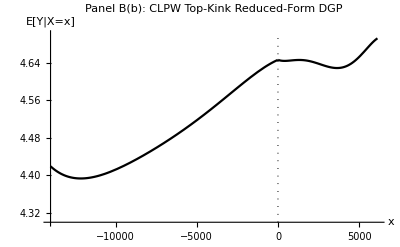

```mathematica
verticalY=Line[{{0,4.3},{0,4.7}}];
DGPTopKinkY=Plot[Piecewise[{{fYl[x],x<0},{fYr[x],x>0}}],{x,-14000,6125},
	PlotStyle-> {Black},
	PlotLabel-> "Panel B(b): CLPW Top-Kink Reduced-Form DGP",
	Axes->True,
	BaseStyle-> {FontFamily-> "Times"},AxesLabel-> {"x","E[Y|X=x]"},
	AxesOrigin->{-14000,4.3},
	PlotRange->{{-14000,6125},{4.3,4.7}},
	Epilog->{Directive[Dotted],verticalY}]
Export["C:/Users/zp53/Dropbox/local poly/graphs/RKD DGP TopKinkY.pdf",DGPTopKinkY, ImageSize->Medium];
```

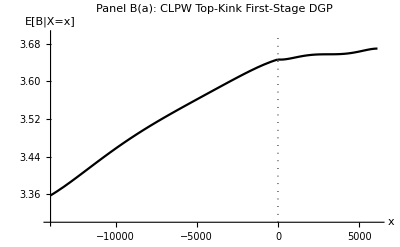

```mathematica
verticalB=Line[{{0,3.3},{0,3.7}}];
DGPTopKinkB=Plot[Piecewise[{{fBl[x],x<0},{fBr[x],x>0}}],{x,-14000,6125},
	PlotStyle-> {Black},
	PlotLabel-> "Panel B(a): CLPW Top-Kink First-Stage DGP",
	Axes->True,
	BaseStyle-> {FontFamily-> "Times"},AxesLabel-> {"x","E[B|X=x]"},
	AxesOrigin->{-14000,3.3},
	PlotRange->{{-14000,6125},{3.3,3.7}},
	Epilog->{Directive[Dotted],verticalB}]
Export["C:/Users/zp53/Dropbox/local poly/graphs/RKD DGP TopKinkB.pdf",DGPTopKinkB, ImageSize->Medium];
```